```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*INIITIALIZE PARAMETERS*)
(*------------------------------------------------------------------------------------------------------------------------------*)

alpha = 0.5;
beta = 1.0;
delta = 0.5;
katta =5;
qAvg = 1.0;
eta = 0.25;
etaBar = 0.5;
chi = 0.1;
uBar = 1.0;
R=20;
T = 100;

(*------------------------------------------------------------------------------------------------------------------------------*)
(*AGENTS*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*Number of firms*)
n = 10.0;

(*Number of consumers*)
m= 100.0;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*PRICING*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*market share of the specialized firm*)
ms[q0_, qi_]:= q0 / Total[qi];

(*markup smart components*)
etaSpec[delta_, etaSpecLag_, q0_, qi_, etaBar_]:=(1-delta)*etaSpecLag + delta*ms[q0,qi]*etaBar;

(*price of specialist*)
pSpec[cs_,etaSpec_]:=(1+etaSpec)*cs;

(*price charged by the firm*)
pFirm[c_,eta_]:=(1+eta)*c;

(*price of firm if it produces the smart component*)
pFirmSelf[cSelf_,eta_]:=(1+eta)*cSelf;

(*price of firm if it produces the smart component*)
pFirmSpec[cSpec_,eta_]:=(1+eta)*cSpec;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*MARGINAL COSTS*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*Marginal costs of the "usual" component*)
cp = 20.0;

(*Marginal costs of the smart component*)
cs = 10.0;

(*Marginal costs if firm buys smart component from specialist*)
cSelf[cp_, cs_]:=cp + cs;

(*Marginal cost if firm buys smart component from specialist*)
cSpec[cp_,cs_, etaSpec_]:=cp + (1+etaSpec)*cs;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*PROFIT*)
(*------------------------------------------------------------------------------------------------------------------------------*)
profit[q_,p_,c_]:=q*p - c*q;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*QUALITY*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*quality of specialist*)
qualitySpec[uBar_, alpha_, beta_,qSpec_ ] :=uBar*(1+ beta*qSpec^alpha);

(*quality of firm*)
qualityFirm[uBar_, alpha_, beta_,qFirm_ ] :=uBar*(1+ beta*qFirm^alpha);
```

```mathematica
(*PROBABILITY*)
probability[i_,priceList_, qualityList_]:=Module[
{p =priceList, u = qualityList},
Exp[-chi*p[[i]]+ katta*u[[i]]]/Sum[Exp[-chi*p[[k]]+ katta*u[[k]]],{k,1,n}]]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*--------------------------------------------------EXERCISE 1-----------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*A: FIXED STRATEGIES: FIRMS PRODUCE SMART COMPONENT*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*Init lists*)
(*------------------------------------------------------------------------------------------------------------------------------*)

priceListAll ={};
qualityListAll ={};
quantitiesAll ={};
profitListAll ={};

(*In the first period quantities produced are equal to zero!*)
qFirmPeriod= Table[0.0,{i,1,n}];
qFirmAggregated=Table[0.0,{i,1,n}];
Id = Table[i,{i,1,n}];

(*------------------------------------------------------------------------------------------------------------------------------*)
(*LOOP*)(*------------------------------------------------------------------------------------------------------------------------------*)

Do[
(*Init lists at each iteration*)
priceList ={};
qualityList ={};
profitList ={};

(*compute prices*)
Do[AppendTo[priceList,pFirmSelf[cSelf[cp,cs],eta]],{i,1,n}];
AppendTo[priceListAll,priceList];

(*compute quality using quantities of last period*)
Do[AppendTo[qualityList,qualityFirm[uBar, alpha, beta,qFirmAggregated[[i]]]],{i,1,n}];
AppendTo[qualityListAll,qualityList];

(*compute probabilities*)
probListAll ={};
Do[
(*Compute all the probabilities for the j-th consumer and append the resulting list to a list that incorporates all these probs!*)
probList = Table[probability[i,priceList, qualityList],{i,1,n}];
AppendTo[probListAll,probList],
{j,1,m}];

(*compute demand*)
choiceListAll = RandomChoice[probList ->Id,m];

(*Compute quantities produced in period t*)
Do[qFirmPeriod[[i]] = Count[choiceListAll,i],{i,1,n}];
(*Compute aggregated quantities in t*)
Do[qFirmAggregated[[i]] = qFirmAggregated[[i]] + qFirmPeriod[[i]] ,{i,1,n}];
AppendTo[quantitiesAll,qFirmAggregated];

(*compute profits*)
Do[AppendTo[profitList,profit[qFirmPeriod[[i]],priceList[[i]],cSelf[cp,cs]]],{i,1,n}];
AppendTo[profitListAll,profitList],
{t,1,5}
];

(*------------------------------------------------------------------------------------------------------------------------------*)
(*Results*)(*------------------------------------------------------------------------------------------------------------------------------*)

Print["Qualities: ",TableForm[qualityListAll]]
Print["Agg. Quantities: ",TableForm[quantitiesAll]]
Print["Profits: ",TableForm[profitListAll]]
```

Qualities: 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
4.16228 | 4.4641 | 4.16228 | 4. | 3.64575 | 4.4641 | 3.82843 | 3.64575 | 4.31662 | 4.74166
4.4641 | 5.89898 | 4.60555 | 4.16228 | 3.64575 | 6.74456 | 3.82843 | 3.64575 | 5.69042 | 9.
4.4641 | 5.89898 | 4.60555 | 4.16228 | 3.64575 | 6.74456 | 3.82843 | 3.64575 | 5.69042 | 13.8062
4.4641 | 5.89898 | 4.60555 | 4.16228 | 3.64575 | 6.74456 | 3.82843 | 3.64575 | 5.69042 | 17.2481

Agg. Quantities: 10. | 12. | 10. | 9. | 7. | 12. | 8. | 7. | 11. | 14.
12. | 24. | 13. | 10. | 7. | 33. | 8. | 7. | 22. | 64.
12. | 24. | 13. | 10. | 7. | 33. | 8. | 7. | 22. | 164.
12. | 24. | 13. | 10. | 7. | 33. | 8. | 7. | 22. | 264.
12. | 24. | 13. | 10. | 7. | 33. | 8. | 7. | 22. | 364.

Profits: 75. | 90. | 75. | 67.5 | 52.5 | 90. | 60. | 52.5 | 82.5 | 105.
15. | 90. | 22.5 | 7.5 | 0. | 157.5 | 0. | 0. | 82.5 | 375.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 750.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 750.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 750.

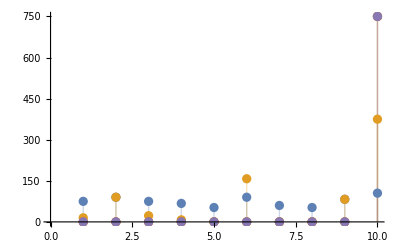

```mathematica
ListPlot[profitListAll,Filling->Axis, PlotRange->All]
```